## Styles and custom color maps

```mathematica
width=2;
framewidth=1.5;
```

```mathematica
fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f)
OpaqueBox[legend_]:=Graphics[{{White,Opacity[0.5],Rectangle[]},Inset[legend,{0.5,0.6},Center]}]
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;
FrameLabelSize = 12;
PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},
LabelStyle->{Directive[Black,FontSize->FrameLabelSize,FontFamily->"Arial"]},
AspectRatio->0.75,ImageSize->400,(*PlotStyle->styles,*)PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[ListLogPlot,PlotOptions];
SetOptions[ListLogLinearPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
SetOptions[ParametricPlot,PlotOptions];
SetOptions[ListStepPlot,PlotOptions];
PlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],PlotPoints->60,MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"}};
SetOptions[Plot3D,PlotOptions3D];
ListPlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"},ColorFunction->"SunsetColors"};
SetOptions[ListPlot3D,ListPlotOptions3D];
DensityPlotOptions = {PlotPoints->60,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[DensityPlot,DensityPlotOptions];
ListDensityPlotOptions = {PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[ListDensityPlot,ListDensityPlotOptions];
```

```mathematica
Legending`LegendDump`$DefaultMarkerStyle=EdgeForm[Opacity[1]];
```

```mathematica
ColorHelix[z_] := Module[{start,rot,gamma,amp,angle,red,green,blue,min,max},
start=0.6;
rot=1.5;  
angle=2.0*Pi*(start/3.0+rot*z);
amp = 0.15;
red=z+amp(-0.14861 Cos[angle]+1.78277Sin[angle]);green=z+amp(-0.29227 Cos[angle]-0.90649Sin[angle]);blue=z+amp(1.97294*Cos[angle]);
RGBColor[Abs[Sqrt[1-red]],Abs[Sqrt[1-green]],Abs[Sqrt[1-blue]]]
]
```

## Definitions and Setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/mnt/workstation/bottomonia_combined_analysis

## Data files

```mathematica
(*output type of the band*)
(*outputType = "output-central";*)
(*outputType = "output-lower";*)
outputType = "OxygenOxygen5360";(*"output-8.16-NP170";*)
```

```mathematica
dataDir="/qtraj_nlo_run1_OO_5.36_kap6_noReg";energy = "5.36";(*energy = "8.16";*)
```

```mathematica
labelMap = Association[
(*{"output_8pPb_Pert_Tf170"-> "TAMU (Γ_pert), T_F = 170 MeV"}*)
(*{"output-5.02-NPWLC170"-> "TAMU (Γ_(NP(WLC))), T_F = 170 MeV"}*)
(*{"qtraj-nlo-run2-00-5.36-kap6-wReg"-> "QTraj-NLO (with Reg), T_F = 180 MeV"}*)
{"qtraj_nlo_run1_OO_5.36_kap6_noReg"-> "QTraj-NLO (No Reg), T_F = 180 MeV"}
(*{"output-8.16-P170"-> "TAMU (Γ_Pert), T_F = 170 MeV"}*)
];
```

```mathematica
keys=Keys[labelMap];
figureNameMap=Table[keys[[i]]->keys[[i]],{i,1,Length[keys]}]//Association;
```

```mathematica
datafile="/inputs/qtraj_inputs/"<>outputType<>"/"<>dataDir<>"/datafile.gz"
```

/inputs/qtraj_inputsOxygenOxygen5360/qtraj_nlo_run1_OO_5.36_kap6_noReg/datafile.gz

```mathematica
(*dirName1=wd<>"/output-"<>energy<>"/"<>figureNameMap[dataDir];
If[!DirectoryQ[dirName1 ],CreateDirectory[dirName1]]*)
```

```mathematica
(*dirName=wd<>"/output-"<>energy<>"/new_formation_time/"<>outputType<>dataDir;*)
dirName=wd<>"/outputs/qtraj_outputs/"<>outputType<>dataDir<>"/"
If[!DirectoryQ[dirName ],CreateDirectory[dirName]]
```

/mnt/workstation/bottomonia_combined_analysis/outputs/qtraj_outputs/OxygenOxygen5360/qtraj_nlo_run1_OO_5.36_kap6_noReg/

```mathematica
wd<>datafile
```

/mnt/workstation/bottomonia_combined_analysis/inputs/qtraj_inputsOxygenOxygen5360/qtraj_nlo_run1_OO_5.36_kap6_noReg/datafile.gz

## Load S and P wave data

```mathematica
rawData=Partition[Import[wd<>datafile,"Table"],2];
Length[rawData]
bVals=rawData[[All,1,1]]//Union
Length[bVals]
```

Import::nffil: File /mnt/workstation/bottomonia_combined_analysis/inputs/qtraj_inputsOxygenOxygen5360/qtraj_nlo_run1_OO_5.36_kap6_noReg/datafile.gz not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

2

Part::partd: Part specification Partition[$Failed,2]⟦All,1,1⟧ is longer than depth of object.

Part::pkspec1: The expression Partition[$Failed,2] cannot be used as a part specification.

1⟦All,Partition[$Failed,2]⟧

3

## Check distribution functions

```mathematica
noFeedDown=IdentityMatrix[9];
```

```mathematica
metaData = rawData[[All,1]];
supData = rawData[[All,2]];
```

Part::partd: Part specification Partition[$Failed,2]⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification Partition[$Failed,2]⟦All,2⟧ is longer than depth of object.

```mathematica
ptData = metaData[[All,5]];(*//Max*)
yData = metaData[[All,7]] ;(*//Min*)
```

Part::partw: Part 5 of Partition[$Failed,2] does not exist.

Part::partw: Part 7 of Partition[$Failed,2] does not exist.

```mathematica
𝒟=HistogramDistribution[yData,40];
testPlot=DiscretePlot[PDF[𝒟,x],{x,-10,10,.01}];
```

HistogramDistribution::invldd: The input data HistogramDistribution[Partition[$Failed,2]⟦All,1⟧⟦All,7⟧] should be a vector or a matrix of real numbers or a valid TemporalData object.

```mathematica
f[y_]:= 0.1(1- 2Sqrt[9.46^2+5^2]/5023 Cosh[y])^(13.8)
(*f2[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/5023 Cosh[y])^(13.8)
f3[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/8160 Cosh[y])^(13.8)*)
```

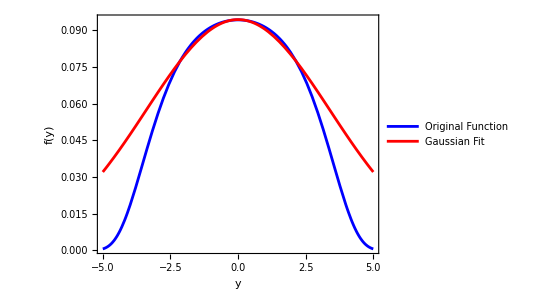

```mathematica
fit[y_]:=0.0944 Exp[-y^2/(2*3.4^2)]
Plot[{f[y],fit[y]},{y,-5,5},PlotLegends->{"Original Function","Gaussian Fit"},PlotStyle->{Blue,Red},PlotRange->All,Frame->True,FrameLabel->{"y","f(y)"}]
```

```mathematica
p2=Plot[{f[y](*,f2[y],f3[y]*)},{y,-7,7},PlotStyle->{Blue,Green,Red}];
(*Show[p1,p2,PlotRange->{{-7,7},All},ImageSize->250]*)
```

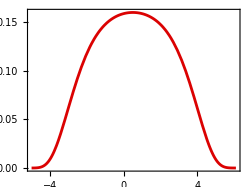

```mathematica
p3=Plot[1.7f[-y+0.5],{y,-5,6.1},PlotStyle->2];
Show[p3,testPlot,ImageSize->250]
```

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] :={x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *)
 sigmasEXP5 = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas5 = Inverse[feeddownMatrix].sigmasEXP5
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### LHC 8 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *)
 sigmasEXP8 = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}*Sqrt[8.16/5.02]
```

{73.4371,24.2241,4.74281,17.4541,20.5267,8.66966,4.16909,15.2994,18.0405}

```mathematica
sigmas8 = Inverse[feeddownMatrix].sigmasEXP8
```

{54.8416,18.8727,4.74281,17.3148,20.4347,8.66966,4.16909,15.2994,18.0405}

#### LHC Choose σ_exp or σ_direct based on Energy

```mathematica
sigmasEXP= If[energy=="5.02",sigmasEXP5,sigmasEXP8]
sigmas = If[energy=="5.02",sigmas5,sigmas8]
```

{73.4371,24.2241,4.74281,17.4541,20.5267,8.66966,4.16909,15.2994,18.0405}

{54.8416,18.8727,4.74281,17.3148,20.4347,8.66966,4.16909,15.2994,18.0405}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.746783

```mathematica
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0679743

```mathematica
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.134334

```mathematica
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.00775625

```mathematica
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0431524

```mathematica
0.7467833958680554+0.0679743142013889+0.13433367881944444+0.007756249999999999+0.043152361111111114
```

1.

## Results as a function of p_T averaged over centrality (with feed down)

### Setup

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] := 1splitHyperfine[x[[2]]]
```

```mathematica
selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax && #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&& #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
weightedList[ptmin_,ptmax_]:=Module[{wtm,temp},
wtm = Mean[selectWeights[ptmin,ptmax]];
 selectPTweighted[ptmin,ptmax]/wtm
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_]:=Mean[weightedList[ptmin,ptmax]]
nAAsdevVsPT[ptmin_,ptmax_]:=StandardDeviation[weightedList[ptmin,ptmax]]/Sqrt[Length[selectPTweighted[ptmin,ptmax]]]
nAAVsPT[ptmin_,ptmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax];
err= nAAsdevVsPT[ptmin,ptmax];
Table[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

### -1.93 < y < 1.93

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
ymin = -1.93;
ymax = 1.93;
```

```mathematica
binwidth=2.5;
ptmax = 30;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Part::partd: Part specification $Failed⟦1,5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

Part::partw: Part 2 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

Part::partw: Part 3 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Part::partw: Part 4 of Mean[Partition[]/Mean[Partition[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{3.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{6.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{8.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{11.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{13.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{16.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{18.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{21.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{23.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{26.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{28.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
naa1p=naavsptData[[All,{1,4,5,6}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
naa2p=naavsptData[[All,{1,8,9,10}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
(*naa1p = naavsptData[[All,{1,4}]] 
naa1p = naavsptData[[All,{1,5}]] 
naa1p = naavsptData[[All,{1,6}]] 
naa2p = naavsptData[[All,{1,8}]]
naa2p = naavsptData[[All,{1,9}]]
naa2p = naavsptData[[All,{1,10}]]*)
```

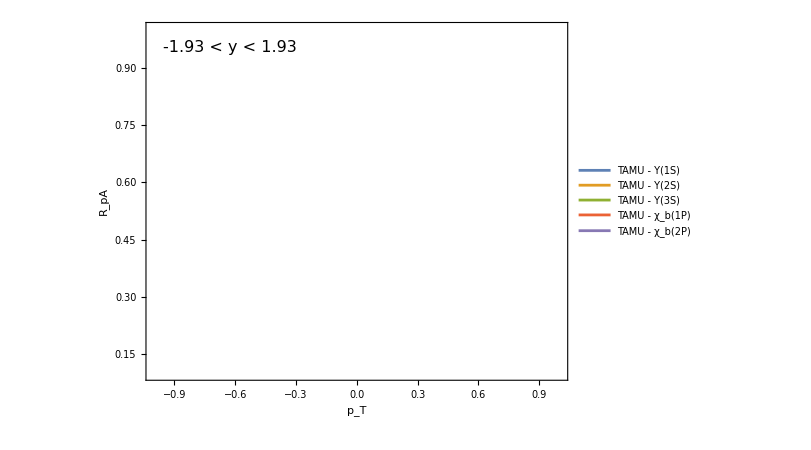

```mathematica
ptpltcen=ListPlot[{naa1s,naa2s,naa3s,naa1p,naa2p },Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_pA"},PlotLegends->Placed[LineLegend[{Style["TAMU - Υ(1S)",16],Style["TAMU - Υ(2S)",16],Style["TAMU - Υ(3S)",16],Style["TAMU - χ_b(1P)",16],Style["TAMU - χ_b(2P)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.1,1.0},Epilog->{Inset[Style[ToString[ymin]<>" < y < "<>ToString[ymax],16],Scaled[{0.2,0.95}],{Center,Top}]}(*,PlotLabel->(*labelMap[dataDir]<>"; "<>*)ToString[ymin]<>" < y < "<>ToString[ymax]*)]
```

```mathematica
fileName =dirName<>"rpavspt-central.m"
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvspt={naa1s,naa2s,naa3s, naa1p,naa2p};
Save[fileName,qtrajRPAvspt]
```

/mnt/workstation/bottomonia_combined_analysis/outputs/qtraj_outputs/OxygenOxygen5360/qtraj_nlo_run1_OO_5.36_kap6_noReg/rpavspt-central.m

### -5 < y < -2.5

```mathematica
ymin = -5;
ymax =-2.5;
```

```mathematica
binwidth=2.5;
ptmax =25; (*pT truncated -- gives large value*)
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

Part::partd: Part specification $Failed⟦1,5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

Part::partw: Part 2 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

Part::partw: Part 3 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Part::partw: Part 4 of Mean[Partition[]/Mean[Partition[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{3.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{6.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{8.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{11.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{13.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{16.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{18.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{21.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{23.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
naa1p=naavsptData[[All,{1,4,5,6}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
naa2p=naavsptData[[All,{1,8,9,10}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
```

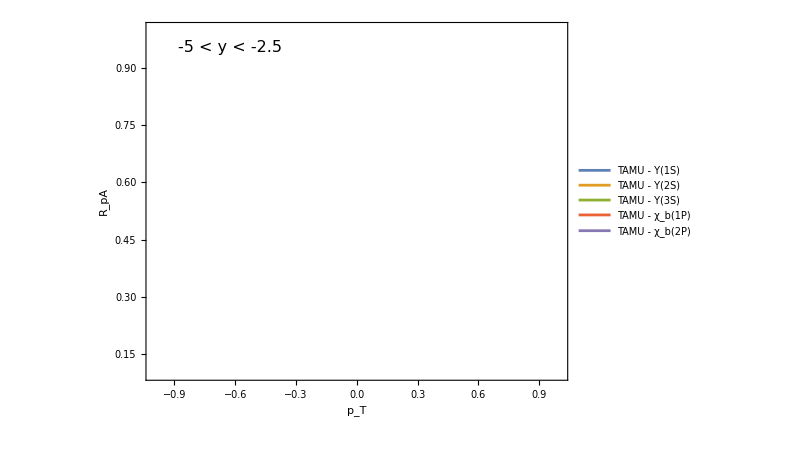

```mathematica
ptpltback=ListPlot[{naa1s,naa2s,naa3s,naa1p,naa2p },Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_pA"},PlotLegends->Placed[LineLegend[{Style["TAMU - Υ(1S)",16],Style["TAMU - Υ(2S)",16],Style["TAMU - Υ(3S)",16],Style["TAMU - χ_b(1P)",16],Style["TAMU - χ_b(2P)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.1,1.0},Epilog->{Inset[Style[ToString[ymin]<>" < y < "<>ToString[ymax],16],Scaled[{0.2,0.95}],{Center,Top}]}(*PlotLabel->(*labelMap[dataDir]<>"; "<>*)ToString[ymin]<>" < y < "<>ToString[ymax]*)]
```

```mathematica
fileName =dirName<>"rpavspt-backward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s,naa1p,naa2p};
Save[fileName,qtrajRPAvspt]
```

### 1.5 < y < 4

```mathematica
ymin = 1.5;
ymax = 4;
```

```mathematica
binwidth=2.5;
ptmax =30;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

Part::partd: Part specification $Failed⟦1,5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

Part::partw: Part 2 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

Part::partw: Part 3 of Mean[Partition[]/Mean[Partition[]]] does not exist.

Part::partw: Part 4 of Mean[Partition[]/Mean[Partition[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{3.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{6.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{8.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{11.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{13.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{16.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{18.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{21.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{23.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{26.25,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧},{28.75,0.0136171 (4.99184 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.0920106 Mean[Partition[]/Mean[Partition[]]]⟦3⟧+6.09482 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+3.67824 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.569597 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0158425 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+1.76402 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.38912 Mean[Partition[]/Mean[Partition[]]]⟦9⟧+(54.8416 Partition[])/Mean[Partition[]])0.0136171 √(3007.6 ComplexInfinity⟦1⟧^2+24.9185 ComplexInfinity⟦2⟧^2+0.00846595 ComplexInfinity⟦3⟧^2+37.1469 ComplexInfinity⟦4⟧^2+13.5295 ComplexInfinity⟦5⟧^2+0.32444 ComplexInfinity⟦6⟧^2+0.000250986 ComplexInfinity⟦7⟧^2+3.11177 ComplexInfinity⟦8⟧^2+1.92966 ComplexInfinity⟦9⟧^2),0.0412813 (0.+18.8727 Mean[Partition[]/Mean[Partition[]]]⟦2⟧+0.918984 Mean[Partition[]/Mean[Partition[]]]⟦6⟧+0.0575334 Mean[Partition[]/Mean[Partition[]]]⟦7⟧+2.76919 Mean[Partition[]/Mean[Partition[]]]⟦8⟧+1.60561 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.0412813 √(356.18 ComplexInfinity⟦2⟧^2+0.844532 ComplexInfinity⟦6⟧^2+0.00331009 ComplexInfinity⟦7⟧^2+7.66842 ComplexInfinity⟦8⟧^2+2.57798 ComplexInfinity⟦9⟧^2),0.210845 (0.+4.74281 Mean[Partition[]/Mean[Partition[]]]⟦3⟧)1. ComplexInfinity⟦3⟧,0.0572932 (0.+17.3148 Mean[Partition[]/Mean[Partition[]]]⟦4⟧+0.139225 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)0.0572932 √(299.804 ComplexInfinity⟦4⟧^2+0.0193835 ComplexInfinity⟦8⟧^2),0.048717 (0.+20.4347 Mean[Partition[]/Mean[Partition[]]]⟦5⟧+0.0920068 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)0.048717 √(417.577 ComplexInfinity⟦5⟧^2+0.00846525 ComplexInfinity⟦9⟧^2),0.115345 (0.+8.66966 Mean[Partition[]/Mean[Partition[]]]⟦6⟧)1. ComplexInfinity⟦6⟧,0.239861 (0.+4.16909 Mean[Partition[]/Mean[Partition[]]]⟦7⟧)1. ComplexInfinity⟦7⟧,0.065362 (0.+15.2994 Mean[Partition[]/Mean[Partition[]]]⟦8⟧)1. ComplexInfinity⟦8⟧,0.0554307 (0.+18.0405 Mean[Partition[]/Mean[Partition[]]]⟦9⟧)1. ComplexInfinity⟦9⟧}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
naa1p=naavsptData[[All,{1,4,5,6}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
naa2p=naavsptData[[All,{1,8,9,10}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
```

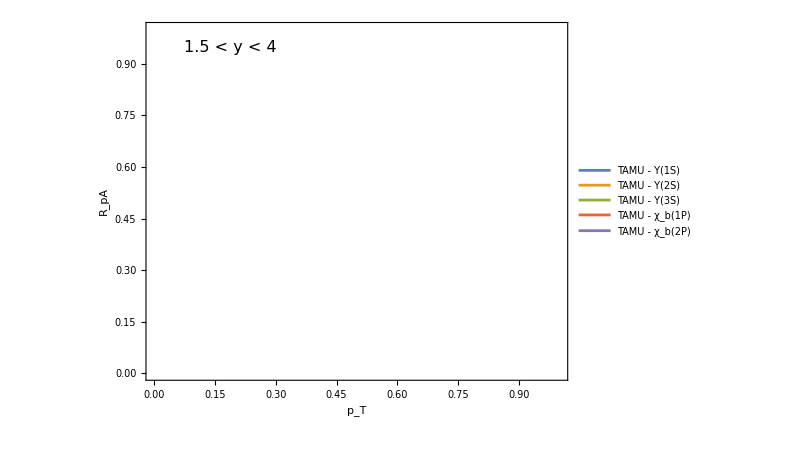

```mathematica
ptpltfor=ListPlot[{naa1s,naa2s,naa3s,naa1p,naa2p },Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_pA"},PlotLegends->Placed[LineLegend[{Style["TAMU - Υ(1S)",16],Style["TAMU - Υ(2S)",16],Style["TAMU - Υ(3S)",16],Style["TAMU - χ_b(1P)",16],Style["TAMU - χ_b(2P)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],Epilog->{Inset[Style[ToString[ymin]<>" < y < "<>ToString[ymax],16],Scaled[{0.2,0.95}],{Center,Top}]}(*PlotRange->{0.1,1.0},PlotLabel->(*labelMap[dataDir]<>"; "<>*)ToString[ymin]<>" < y < "<>ToString[ymax]*)]
```

```mathematica
fileName =dirName<>"rpavspt-forward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s,naa1p,naa2p};
Save[fileName,qtrajRPAvspt]
```

## Results as a function of y averaged over centrality and p_T (with feed down)

#### Setup

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] :=  1*splitHyperfine[ x[[2]] ]
```

```mathematica
selectWeights[ymin_,ymax_]:=getWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
selectYweighted[ymin_,ymax_]:=mapWithWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
weightedList[ymin_,ymax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ymin,ymax]];
res = selectYweighted[ymin,ymax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsY[ymin_,ymax_]:= Module[{wl,num,qweights},
wl=weightedList[ymin,ymax];
qweights = ConstantArray[1,Length[wl]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsY[ymin_,ymax_]:=Module[{wl},
wl = weightedList[ymin,ymax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsY[ymin_,ymax_]:=Module[{avg,err},
avg = nAAavgVsY[ymin,ymax];
err= nAAsdevVsY[ymin,ymax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Results

```mathematica
binwidth=0.5;
ymax =5.0; (* error here*)
(* flip y here due to inverse in hydro setup *)
npavsyData=Reverse[Table[Join[{-x+-binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N]
```

Part::partd: Part specification $Failed⟦1,7⟧ is longer than depth of object.

Part::partd: Part specification 2⟦1,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in Append.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

General::stop: Further output of Partition::argb will be suppressed during this calculation.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::take: Cannot take positions 1 through 9 in Append.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 4 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 5 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 6 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 7 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 8 of 1/2 MapThread.{1,1} does not exist.

Part::partw: Part 9 of 1/2 MapThread.{1,1} does not exist.

MapThread::mptd: Object Partition[]/Mean[Partition[]] at position {2, 1} in MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}] has only 0 of required 1 dimensions.

Part::partw: Part 3 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 4 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 5 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 6 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 7 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 8 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Part::partw: Part 9 of StandardDeviation[MapThread[Append,{Partition[]/Mean[Partition[]],Partition[]}]]/(√2) does not exist.

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

```mathematica
Reverse[Table[Join[{-x+-binwidth/2},noFeedDown.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N]
```

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
npa1s =npavsyData[[All,{1,2}]] ;
npa2s = npavsyData[[All,{1,3}]] ;
npa3s = npavsyData[[All,{1,7}]] ;
(*
npa1p = npavsyData[[All,{1,4}]] 
npa1p = npavsyData[[All,{1,5}]] 
npa1p = npavsyData[[All,{1,6}]] 
npa2p=npavsyData[[All,{1,8}]]
npa2p=npavsyData[[All,{1,9}]]
npa2p=npavsyData[[All,{1,10}]]
*)
npa1p=npavsyData[[All,{1,4,5,6}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
npa2p=npavsyData[[All,{1,8,9,10}]]/. {x_,c4_,c5_,c6_}:>{x,Mean[{c4,c5,c6}]};
```

```mathematica
yPlot=ListPlot[{npa1s,npa2s,npa3s, npa1p, npa2p},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"y","R_pA"},PlotLegends->Placed[LineLegend[{Style["Υ(1S)",16],Style["Υ(2S)",16],Style["Υ(3S)",16],Style["χ_b(1P)",16],Style["χ_b(2P)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{{-5.0,5.0},{0.1,1.0}},Epilog->{Inset[Style[labelMap[outputType ],15],Scaled[{0.35,0.95}],{Center,Top}]}(*PlotLabel->labelMap[outputType ]*)]
```

```mathematica
fileName =dirName<>"rpavsy.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvsy={npa1s,npa2s,npa3s,npa1p,npa2p};
Save[fileName,qtrajRPAvsy]
```

```mathematica
(*Export[dirName<>"rpa-hnm-y.pdf",yPlot]*)
```

```mathematica
allplt=GraphicsGrid[{{yPlot,ptpltcen},{ptpltfor,ptpltback}},ImageSize->1200]
Export[dirName<>"/rpa-hnm-all.pdf",allplt]
```

#### Results - integrate

```mathematica
binwidth=10;
ymax =5;
(* flip y here due to inverse in hydro setup *)
naavsyData=Reverse[Table[Join[{-x+-binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N]
```

```mathematica
naavsyData[[1]][[3]]/naavsyData[[1]][[2]]
naavsyData[[1]][[7]]/naavsyData[[1]][[2]]
```

```mathematica
a={{0.,0.847160.00009,0.638070.00021,0.681440.00026,0.680740.00026,0.681040.00026,0.651140.00025,0.593060.00027,0.593060.00027,0.593060.00027}};
```

```mathematica
a[[1]][[3]]/a[[1]][[2]]
a[[1]][[7]]/a[[1]][[2]]
```